# Analiza podjetja Nvidia

## Pridobivanje podatkov

Podjetje NVIDIA se ukvarja s proizvajanjem polprevodnikov, najbolj znana je po svojih grafičnih karticah. V spodnji tabeli so podatki podjetja.

```mathematica
CompanyData[Entity["Company","NVIDIACorporation::7ymsk"], "Dataset"]
```

Spodnji ukaz izriše graf, ki nam pove “Gross profit”, kar je vrednost dobička s prodajo z odštetimi stroški prodaje (TTM...zadnjih dvanajst mesecev, Quarterly...četrtletje, Annual...letno). 
Pove nam kako učinkovito podjetje uporablja svojo delovno silo in zaloge za proizvodnjo produktov ali storitev.

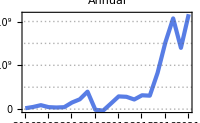
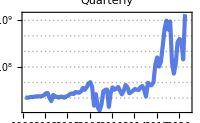
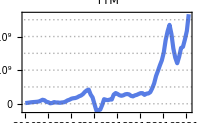

```mathematica
DateListPlot[Entity["Company","NVIDIACorporation::7ymsk"][EntityProperty["Company","NetIncome",{"TimeSeriesType"->#,"Date"->All}]],ImageSize->200,PlotLabel->#, PlotTheme->"Business"]&/@{"Annual","Quarterly","TTM"}
```

Največji tekmec Nvidie je podjetje AMD, zato si poglejmo kako izgleda "gross profit" AMDja :

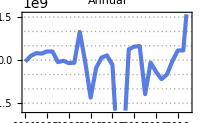
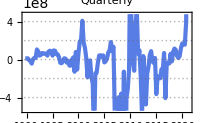
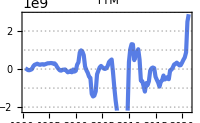

```mathematica
Row[DateListPlot[Entity["Company","AdvancedMicroDevices::7739t"][EntityProperty["Company","NetIncome",{"TimeSeriesType"->#,"Date"->All}]],ImageSize->200,PlotLabel->#, PlotTheme->"Business"]&/@{"Annual","Quarterly","TTM"}]
```

## Primerjava z največjim tekmecem

Primerjajmo čisti dobiček (odšteti čisto vsi stroški) podjetja AMD s podjetjem Nvidia.

```mathematica
Nvidia = Entity["Company","NVIDIACorporation::7ymsk"][EntityProperty["Company","NetIncome",{"TimeSeriesType"->#,"Date"->All}]]&/@{"TTM"}
```

{TimeSeries[…]}

```mathematica
Amd = Entity["Company","AdvancedMicroDevices::7739t"][EntityProperty["Company","NetIncome",{"TimeSeriesType"->#,"Date"->All}]]&/@{"TTM"}
```

{TimeSeries[…]}

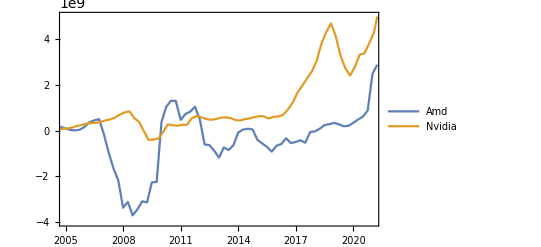

```mathematica
DateListPlot[{Amd ,Nvidia}, PlotRange->{{{2005,1,1},{2021,1,1}},{-4*10^9,5*10^9}} ,PlotLegends->{"Amd","Nvidia"}]
```

Vidimo, da ima Nvidia trenutno veliko več dobička kot AMD, sploh v zadnjih 5 letih. Poglejmo si še logaritmično krivuljo.

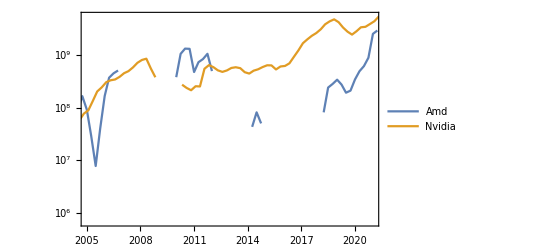

```mathematica
DateListLogPlot[{Amd ,Nvidia}, PlotRange->{{{2005,1,1},{2021,1,1}},Automatic} ,PlotLegends->{"Amd","Nvidia"}]
```

Zgoraj vidimo, da je po logaritmični krivulji Nvidia prehitela AMD okoli leta 2012
Poglejmo si še graf obeh delnic

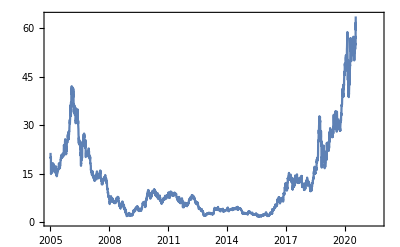

```mathematica
DateListPlot[FinancialData[LinguisticAssistant,"Jan. 1, 2005"]]
```

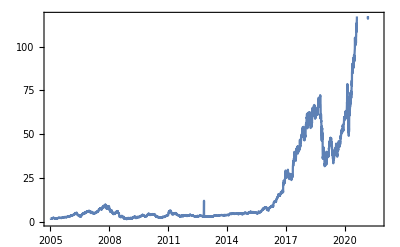

```mathematica
DateListPlot[FinancialData[LinguisticAssistant,"Jan. 1, 2005"]]
```

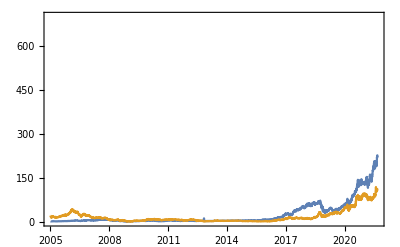

```mathematica
DateListPlot[{FinancialData[LinguisticAssistant,"Jan. 1, 2005"], FinancialData[LinguisticAssistant,"Jan. 1, 2005"]}, PlotRange-> {0,700}]
```

Za boljši  prikaz si poglejmo logaritemsko krivuljo.

DateListLogPlot[{FinancialData["NVIDIA","Jan. 1, 2000"], FinancialData["Advanced Micro Devices Inc","Jan. 1, 2000"] }, PlotLegends →  {"Nvidia", "AMD"},PlotRange→ {0,700}]

Vidimo,  da je AMD po rasti svoje delnice prehiteval Nvidio pred letom 2005, približno leta 2007 pa se je zadeva obrnila.

Poglejmo si net margin, ki nam pove razliko med čistim dobičkom in celotnimi prihodki in je eden izmed ključnih pokazateljev uspešnosti podjetja.

```mathematica
companyTS = 
  EntityValue[{LinguisticAssistant,LinguisticAssistant}, 
   Dated[{"TotalRevenue", "GrossProfit", "OperatingIncome", 
     "NetIncome"}, 
    Interval[{DateObject[{2014, 1, 1}], DateObject[{2019, 1, 1}]}]], 
   "EntityAssociation"];
```

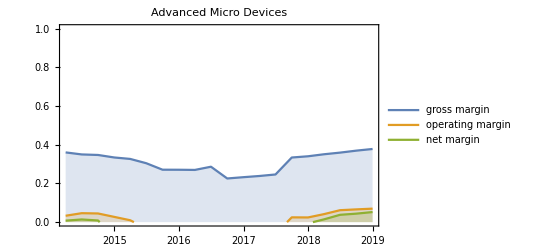
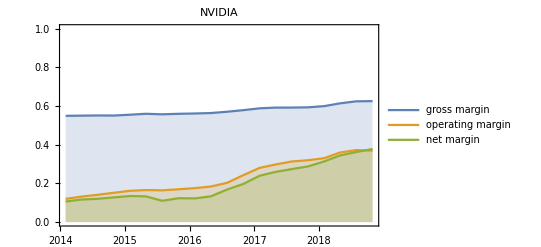
-Graphics- | -Graphics-

```mathematica
Multicolumn[With[{data=#/.companyTS},DateListPlot[{data[[2]]/data[[1]],data[[3]]/data[[1]],data[[4]]/data[[1]]},PlotRange->{Full,{0,1}},Filling->Bottom,PlotLabel->#,PlotLegends->{"gross margin","operating margin","net margin"}]]&/@{LinguisticAssistant,LinguisticAssistant},2]
```

## Geografska analiza podjetja

Poglejmo si katera podjetja so v okolici Nvidije (Nvidia je v sredini zemljevida)

```mathematica
EntityPrefetch[EntityProperty["Company","Position"]]
pos=Entity["Company","NVIDIACorporation::7ymsk"]["Position"];
```

Success[…]

```mathematica
nearbyCompanies=EntityList[FilteredEntityClass["Company",EntityFunction[c,!MissingQ[c["Position"]]&&GeoDistance[c["Position"],pos]<Quantity[10,"Miles"]]]];
Length[nearbyCompanies]
(*944*)
```

948

```mathematica
netIncomeList=Select[DeleteMissing[EntityValue[nearbyCompanies,{"Position","NetIncome"},"EntityAssociation"],1,∞],QuantityMagnitude[Last[#]]>0&];
Length[netIncomeList]
(*80*)
```

81

```mathematica
TableForm[Normal[TakeLargestBy[netIncomeList,Last,10]]/.Rule->List]
```

Apple | GeoPosition[{37.3317,-122.031}]
7.6311×10^10 $
Alphabet | GeoPosition[{37.423,-122.084}]
5.1363×10^10 $
Intel | GeoPosition[{37.3886,-121.963}]
1.8599×10^10 $
Cisco Systems | GeoPosition[{37.4095,-121.953}]
1.0218×10^10 $
Adobe | GeoPosition[{37.3301,-121.894}]
5.566×10^9 $
NVIDIA | GeoPosition[{37.3646,-121.968}]
5.327×10^9 $
PayPal Holdings | GeoPosition[{37.2969,-121.819}]
5.215×10^9 $
Applied Materials | GeoPosition[{37.3646,-121.968}]
4.432×10^9 $
Broadcom | GeoPosition[{37.2969,-121.819}]
3.953×10^9 $
Netflix | GeoPosition[{37.233,-121.951}]
3.75904×10^9 $

```mathematica
geoNetList=Rule@@@Values[netIncomeList];
Show[GeoGraphics[{EdgeForm[Black],Red,GeoDisk[pos,Quantity[10,"Miles"]]}],GeoBubbleChart[geoNetList,GeoRangePadding->Quantity[2,"Miles"]]]
```

-Graphics-

Kot vidimo ima največji čisti dobiček Apple. AMD je na enaki lokaciji kot Nvidija, le da ima tako nizek čisti dobiček, da ga ni na naši mapi.

### Proizvodnja v Taiwanu

Nvidia ima tovarne za proizvodnjo čipov v Taiwanu. Poglejmo si kateri podatki so na voljo.

```mathematica
CountryData[Entity["Country","Taiwan"], "Dataset"]
```

Ker se iz takega prikaza ne da nič razbrati si podatke poglejmo na drugačen način.

```mathematica
p=CountryData["Properties"];
```

```mathematica
l=Table[{i,Quiet@Check[CountryData["Taiwan",{i,All}],Missing["NotAvailable"]]},{i,p}];
lt=Select[l,#[[2]]=!=Missing["NotAvailable"]&];
Length@lt (*25*)
```

25

```mathematica
Quiet@Animate[Check[DateListPlot[lt[[x,2]],PlotLabel->lt[[x,1]]],"OPPS"],{x,1,Length@lt,1}]
```

Kot vidimo na Wolframu ni veliko podatkov o Taiwanu. Znano je, da na ceno čipov zelo negativno vpliva suša. Poglejmo si graf padavin Taiwana.

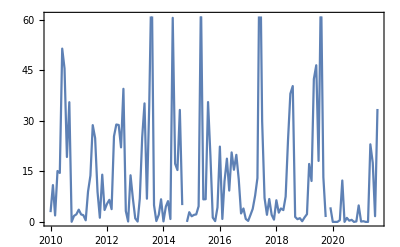

```mathematica
DateListPlot[WeatherData["Taiwan","TotalPrecipitation",{{2010,1,1},{2021,12,31},"Month"}],Joined->True]
```

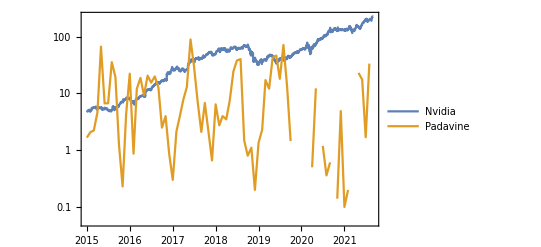

```mathematica
DateListLogPlot[{FinancialData[Entity["Financial","NASDAQ:NVDA"],"Jan. 1, 2015"], WeatherData["Taiwan","TotalPrecipitation",{{2015,1,1},{2021,12,31},"Month"}] }, PlotLegends ->  {"Nvidia", "Padavine"},PlotRange-> Automatic,Joined->True]
```

## Aplikacija v oblaku

Aplikacija bo primerjala grafe vnešene delnice z Nvidijino delnico.

```mathematica
MakeGraph[stock_]:=Show[DateListLogPlot[{FinancialData[Entity["Financial","NASDAQ:NVDA"],"Jan. 1, 2018"],FinancialData[stock,"Jan. 1, 2018"]},PlotLegends->{"Nvidia",EntityValue[stock,"Name"]},PlotRange->{0,700}]]
```

```mathematica
ob=FormPage["stock"->"Financial",MakeGraph[#stock]&,AppearanceRules-><|"Title"->"Comparison of two stocks","Description"->"Input the name of the company to compare it to Nvidia stock","SubmitLabel"->"Submit"|>]
```

```mathematica
CloudDeploy[ob, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/fcc4bd37-9d23-47d0-9c91-64142ec4db57]

WolframAlphaQueryResults

AMD

```mathematica
Entity["Financial","NASDAQ:AMD"]
```